```mathematica
test=Import["Data/Final/ApplicationExamples.mx"];
```

Global`GraphicsColor::shdw: Symbol GraphicsColor appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`LineColor::shdw: Symbol LineColor appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`FrontFaceColor::shdw: Symbol FrontFaceColor appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

```mathematica
NExtractAndApply[#] & /@ test;
```

$Aborted

```mathematica
keys = Keys @ fullAssociation;
values = Values @Values @fullAssociation;
```

Keys::invrl: The argument fullAssociation is not a valid Association or a list of rules.

Values::invrl: The argument fullAssociation is not a valid Association or a list of rules.

Values::invrl: The argument Values[fullAssociation] is not a valid Association or a list of rules.

```mathematica
Get["../FunctionAnalysisPackage.m"]
```

```mathematica
fa = FAGenerateAssociation[];
```

```mathematica
ico =Iconize[fa, "Full association of all symbols"];
```

```mathematica
Position[#, Max[#]]&@VertexDegree[graph]
```

{{3348}}

```mathematica
VertexList[graph][[3348]]
```

List

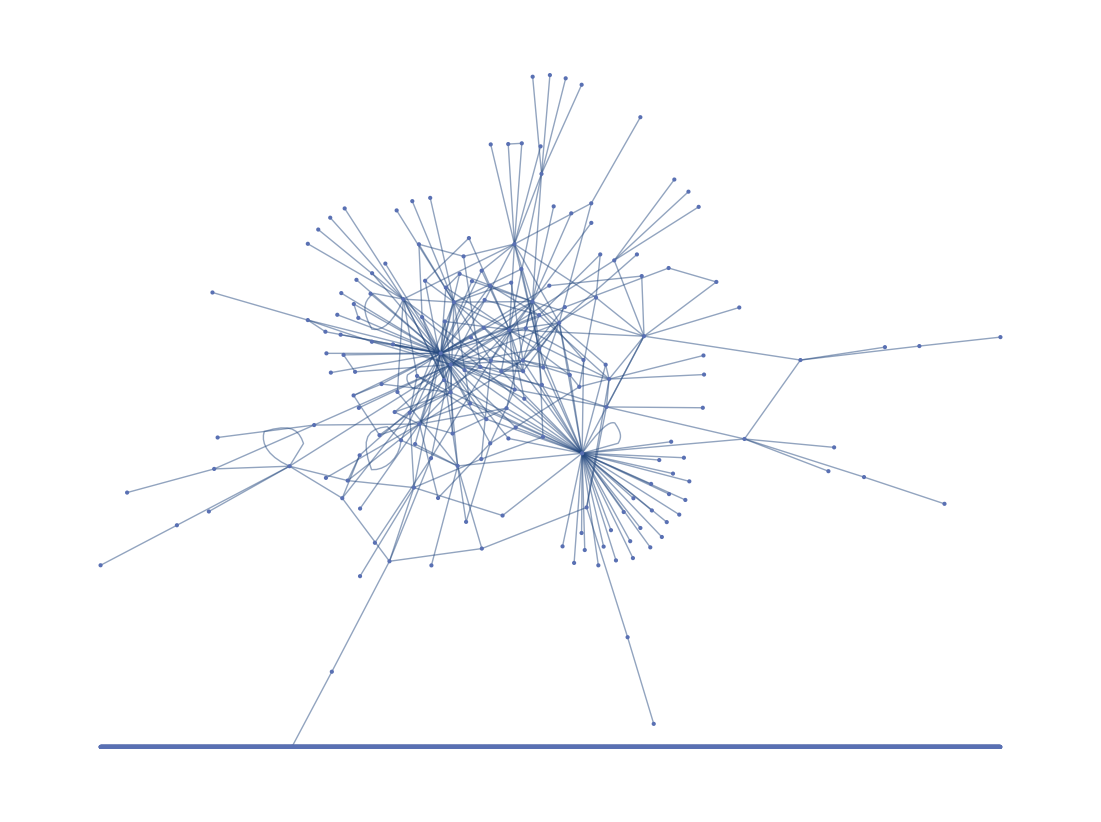

```mathematica
graph = AdjacencyGraph[keys, values, DirectedEdges->False, VertexLabels->Placed[Automatic,Tooltip]]
```

```mathematica
vdegree = VertexDegree[graph];
```

```mathematica
weight=AssociationThread[keys, 1/ (Log[vdegree]+1)];
```

```mathematica
Reverse @ Sort[weight // N] // Dataset
```

Dataset[<>]

```mathematica
Foo[association, ]
```

```mathematica
nf=Nearest[Names["System`*"]];
suggestionFunction[str_]:=First[nf[str],$Failed]
suggestionBox[str_]:=With[
{s=suggestionFunction[str]},
If[FailureQ[s],
"No match found",
"Did you mean "<>s<>"?"
]
]
```

```mathematica
DynamicModule[{str = "Probability", res = "", fd, useW},
Deploy@Column[{
	"Input a function name", 
	InputField[Dynamic[str], String],
	"\n",
	Row[{"Use weight: ",Checkbox[Dynamic[useW]]}],
	"\n",
	Button["Compute",
		If[MissingQ[fullAssociation[[str]]], 
			res = suggestionBox[str],
			With[	
				{(*mf= Map[FindMaximumFlow[graph, str, #] &, Keys @ fullAssociation[[str]]]*) (* Used FindMinimumCostFlow *)
				w = Map[fullAssociation[[str]][[#]] * If[useW, weight[[#]], 1] &, Keys @ fullAssociation[[str]]]
				(*w = PageRankCentrality[graph, weight]*)},
				res = Column @ {
					"Function: "<>str,
					fd = Select[AssociationThread[Keys @ fullAssociation[[str]], w ], #>0&];,
					 Reverse @ Sort[fd // N] // Dataset
					(*Select[fd, # ≥ Median[fd]&]*)
					(*"Mean: "<>ToString[Mean[fd]]*)
				}
			]
		]
	],
	Dynamic[res]
}]
]
```

```mathematica
Select[fullAssociation["RiceDistribution"], # >0&]
```

<||>

```mathematica
FindShortestPath[graph, "GaussianFilter", "Blur"]
```

{GaussianFilter,Image,Blur}

```mathematica
FAExtractWCount[HoldComplete[Sin[Cos[x]]]]
```

<|Sin→<|Cos→1|>,Cos→<||>|>

```mathematica
Get["../FunctionAnalysisPackage.m"]
```

```mathematica
f[x_] = x;
```

```mathematica
fa =  FAGenerateAssociation[];
```

```mathematica
FAExtractAndApplyTo[fa, Import["/home/pb/Dropbox/WSS19/SummerSchool2019/Final Project/Drafts/NotebookBar.m", "HeldExpressions"]]
```

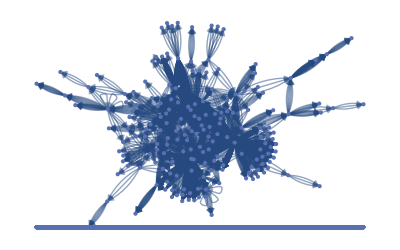

```mathematica
g = FAGenerateGraph[fa, True]
```

```mathematica
Foo[x_] :=((x+1) / (Max[x]+1))^-1;

w = FAGenerateWeights[g, fa, Foo]
```

<|a→1054,b→1054,c→1054,d→1054,e→1054,f→1054,g→1054,h→1054,i→1054,j→1054,k→1054,l→1054,6537,$UserAgentVersion→1054,$UserBaseDirectory→1054,$UserDocumentsDirectory→1054,$Username→1054,$UserName→1054,$UserURLBase→1054,$Version→527/2,$VersionNumber→527/5,$VoiceStyles→1054,$WolframID→1054,$WolframUUID→1054,\[SystemsModelDelay]→1054|>
 |  |  |  |

```mathematica
Reverse @ Sort[FAFindCommonWith["If", w, fa]] // Dataset
```

Dataset[<>]

```mathematica
Foo[x_] := 1/x;
```

```mathematica
Bar[x_, f_] := f[x]
```

```mathematica
Bar[2,Foo]
```

1/2

```mathematica
test = Import["/home/pb/Dropbox/WSS19/SummerSchool2019/Final Project/Drafts/NotebookBar.m", "HeldExpressions"];
```

```mathematica
FAFindCommonWith["Button", test]
```

<|CompoundExpression→6/(1+Log[75]),CopyToClipboard→3/(1+Log[7]),Dynamic→4/(1+Log[24]),FrontEndTokenExecute→1/(1+Log[4]),Graphics→5/(1+Log[29]),If→1/(1+Log[37]),Magnify→1,Rule→33/(1+Log[297]),SetOptions→3/(1+Log[32]),Style→3/(1+Log[14])|>